Reproduce Ogasawara et al. [2017] plots, make sure they real

### The function, equation (1)

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_,mass_]:=n (mass/(2 π kappa T (1-3/(2 kappa))))^(3/2)2/mass^2 Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

#### After Spence has had his way

n in cm^-3
T in keV
energy in keV
phi0 in keV

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

Energy “pre-shifted” by phi0

```mathematica
OgasaFuncShift[en_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

## Ogasawara-related stuff

### Parameters for Arc1

```mathematica
phi0=83/10; (*kV*)
T=14/10; (*keV*)
n=6/10; (*cm^-3*)
kappa=21;
```

```mathematica
fluxdivE={1*^7,7*^6,1.2*^6,6*^5,1.5*^5,5*^4,1.9*^4,1.2*^3,8*^1,9,4};
EminusPhi={2,4,6,7.5,9,11,13,18,21,31,39};
```

```mathematica
ogasaDat=Partition[Riffle[EminusPhi,fluxdivE],2]
```

{{2,10000000},{4,7000000},{6,1.2×10^6},{7.5,600000},{9,150000.},{11,50000},{13,19000.},{18,1200.},{21,80},{31,9},{39,4}}

```mathematica
ogasaModelDat=OgasaFuncShift[en,T,kappa,n];
```

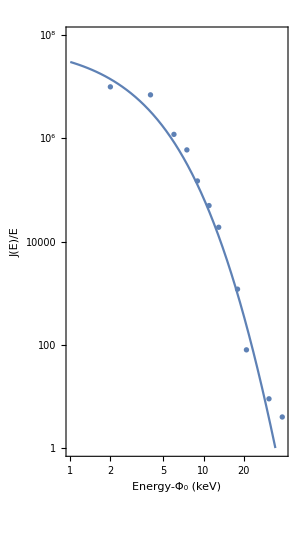

```mathematica
Show[LogLogPlot[ogasaModelDat,{en,1,40},PlotRange->{{1,40},{1,1*^8}},Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300],ListLogLogPlot[ogasaDat]]
```

### Try to fit Ogasawara myself

```mathematica
constraints={0.3<ogN<4,0.1<ogT<3,4<ogKappa<35};
ogModel = OgasaFuncShift[en,ogT,ogKappa,ogN];
```

```mathematica
fitter=FindFit[fluxdivE,{ogModel,constraints},{ogT,ogKappa,ogN},en]
```

{ogT→0.399618,ogKappa→4.,ogN→0.3}

```mathematica
fitter={ogT->1.418691778862197,ogKappa->35.,ogN->0.51152979714127504}
```

{ogT→1.41869,ogKappa→35.,ogN→0.51153}

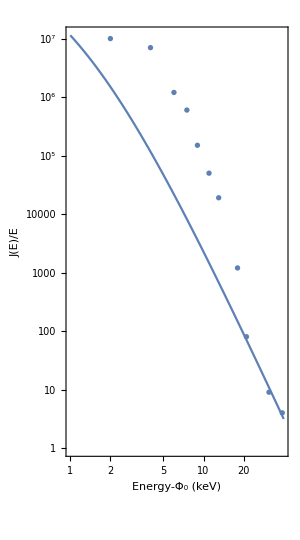

```mathematica
Show[LogLogPlot[ogModel/.fitter,{en,1,40},Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300],ListLogLogPlot[ogasaDat]]
```

## FAST-related stuff

```mathematica
Needs["ErrorBarPlots`"]
```

#### Now a function for FAST

n in cm^-3, T in eV, Φ_0 in eV, en in eV

```mathematica
OgasaFuncFAST[en_,phi0_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
OgasaFuncFASTShift[en_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
OgasaFuncFASTShiftkeV[en_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^7)/(√1022)Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

### Other helper functions

```mathematica
makeErrorDataOld[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
errorB=Map[ErrorBar,errorsDivE];
zeList=Partition[Riffle[eAndFlux,errorB],2]
];
```

```mathematica
makeErrorData[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
zeList=Partition[Flatten[Riffle[eAndFlux,errorsDivE]],3]
];
```

```mathematica
makeLogErrorData[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList,eAndFlux,tmpList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
tmpList=Partition[Flatten@Riffle[eAndFlux,errorsDivE],3];
zeList={{Log10[#[[1]]],Log10[#[[2]]]},ErrorBar[Log10[1+0.5#]&/@{-#[[3]]/#[[2]],#[[3]]/#[[2]]}]}&/@tmpList
];
```

```mathematica
LogErrorListPlot[errorData_]:=Module[{logErrorPlot,plotrange,xticks,yticks,xt,yt,logData},
plotrange={Floor@Log10@Min[#],Ceiling@Log10@Max[#]}&@errorData[[All,#]]&/@{1,2};
xticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[1]];
yticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[2]];
{xt,yt}=#~Join~({#,""}&/@Flatten[(#[[1]]+Log10[{2,3,4,5,6,7,8,9}])&/@#])&/@{xticks,yticks};
logData={{Log10[#[[1]]],Log10[#[[2]]]},ErrorBar[Log10[1+0.5#]&/@{-#[[3]]/#[[2]],#[[3]]/#[[2]]}]}&/@errorData;
logErrorPlot=ErrorListPlot[logData,Joined->True,PlotRange->plotrange,FrameTicks->{{yt,None},{xt,None}},GridLines->{xt[[All,1]],yt[[All,1]]},Frame->True,Axes->False,FrameLabel->{"Energy (eV)","J(E)/E"},FrameStyle->(FontSize->18),AspectRatio->14/10,ImageSize->500]
];
```

### Data from my arc

```mathematica
energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,2.208*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,6.748,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,4.772,2.489};
```

```mathematica
(*energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,1.806*^4,2.208*^4,2.609*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,0.000,6.748,0.000,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,0.000,4.772,0.000,2.489};*)
```

```mathematica
spenceDat=makeErrorDataOld[energies,flux/energies,errors/energies];
```

```mathematica
spenceLogDat=makeErrorData[Log10[energies],Log10[flux/energies],Log10[errors/energies]]
```

{{2.91137,2.94068,1.51514},{2.9735,2.88654,1.426},{3.05269,2.59224,1.19967},{3.13988,2.08903,0.860555},{3.21245,1.57832,0.532465},{3.27462,1.12401,0.24284},{3.35372,0.659956,-0.0724633},{3.44091,0.145003,-0.416423},{3.51335,-0.163685,-0.647832},{3.57553,-0.480016,-0.873448},{3.65475,-1.0227,-1.2704},{3.74186,-1.12079,-1.4282},{3.81445,-1.52709,-1.71167},{3.87656,-1.84073,-2.06559},{3.95578,-2.43766,-2.60341},{4.04297,-2.74107,-2.83533},{4.11561,-3.3564,-3.3564},{4.17754,-3.48048,-3.48048},{4.344,-3.51482,-3.6653},{4.47871,-4.08269,-4.08269}}

```mathematica
showError=1;
```

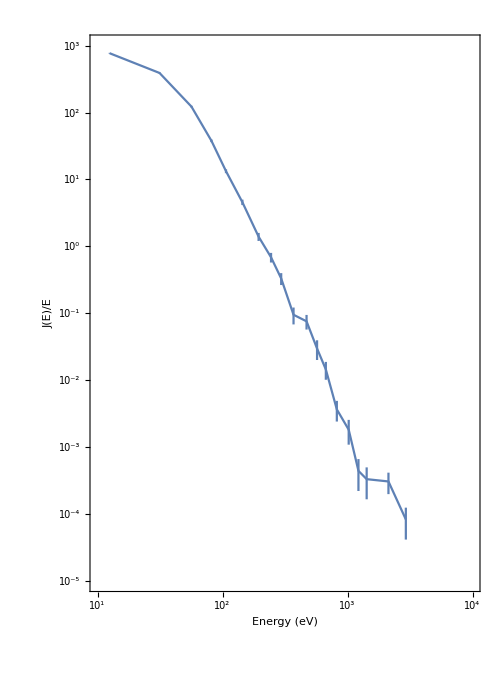

```mathematica
LogErrorListPlot[makeErrorData[(energies[[2;;]]-energies[[1]])/10,flux[[2;;]]/energies[[2;;]],errors[[2;;]]/energies[[2;;]]]]
```

```mathematica
phi0=940;
T=353;
kappa=163/100;
dens=0.28;
```

```mathematica
modelData=Partition[Riffle[energies,OgasaFuncFAST[energies,phi0,T,kappa,dens]],2]
```

{{815.4,-717.738-1658.6 ⅈ},{940.8,7136.97},{1129.,101.906},{1380.,15.0653},{1631.,5.03853},{1882.,2.33071},{2258.,0.997936},{2760.,0.437665},{3261.,0.234145},{3763.,0.141184},{4516.,0.0764844},{5519.,0.040212},{6523.,0.0239862},{7526.,0.0155835},{9032.,0.00909759},{11040.,0.00509365},{13050.,0.00316653},{15050.,0.00212133},{22080.,0.000734632},{30110.,0.000315496}}

```mathematica
logModelData={{Log10[#[[1]]],Log10[#[[2]]]}}&/@modelData;
```

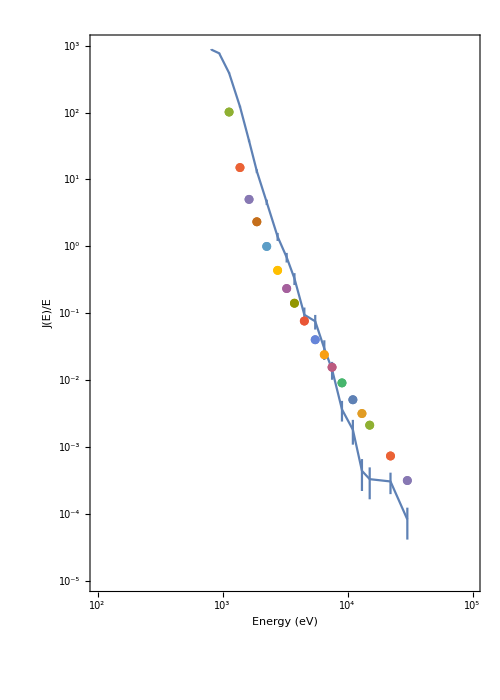

```mathematica
Show[LogErrorListPlot@makeErrorData[energies,flux/energies,errors/energies],ListPlot[logModelData,InterpolationOrder->3]]
```

### Fits

```mathematica
constraints={0.001<fitN<4,10<fitT<5000,1.51<fitKappa<35};
```

```mathematica
FASTModel = OgasaFuncFASTShift[en,fitT,fitKappa,fitN];
```

```mathematica
eAndFlux=Partition[Riffle[energies[[3;;]]-energies[[2]],flux[[3;;]]/energies[[3;;]]],2];
```

```mathematica
fitter=FindFit[eAndFlux,{FASTModel,constraints},{fitT,fitKappa,fitN},en]
```

{fitT→222.135,fitKappa→34.9986,fitN→0.565268}

```mathematica
fitter={fitT->222.1346149321158,fitKappa->1.8,fitN->0.565};
```

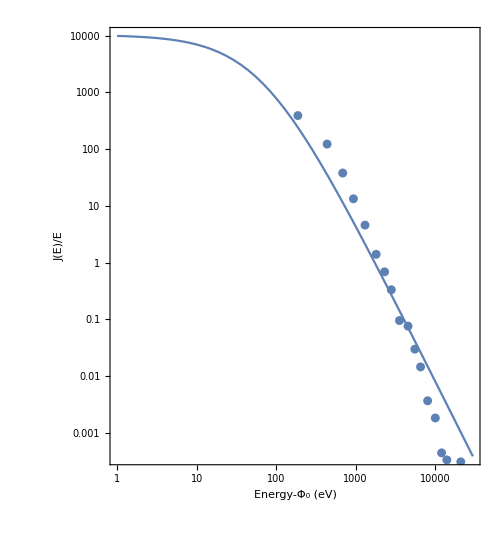

```mathematica
Show[LogLogPlot[FASTModel/.fitter,{en,1,30000},Frame->True,FrameLabel->{"Energy-Φ_0 (eV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->11/10,ImageSize->500],ListLogLogPlot[eAndFlux]]
```

#### Try keV energies

```mathematica
startInd=3;
```

```mathematica
constraints={0.001<fitN<4,0.02<fitT<5,1.51<fitKappa<35};
```

```mathematica
FASTModelkeV = OgasaFuncFASTShiftkeV[en,fitT,fitKappa,fitN];
```

```mathematica
eAndFluxkeV=Partition[Riffle[(energies[[startInd;;]]-energies[[startInd-1]])/1000,flux[[startInd;;]]/energies[[startInd;;]]*1000],2];
```

```mathematica
eAndFluxkeV
```

{{0.1882,391054.},{0.4392,122754.},{0.6902,37872.5},{0.9412,13305.},{1.3172,4570.42},{1.8192,1396.38},{2.3202,685.986},{2.8222,331.119},{3.5752,94.907},{4.5782,75.7202},{5.5822,29.7103},{6.5852,14.43},{8.0912,3.65035},{10.0992,1.81522},{12.1092,0.440153},{14.1092,0.330764},{21.1392,0.305616},{29.1692,0.0826636}}

```mathematica
fitter=FindFit[eAndFluxkeV,{FASTModelkeV,constraints},{fitT,fitKappa,fitN},en]
```

{fitT→0.222134,fitKappa→35.,fitN→0.565268}

```mathematica
fitter={fitT->0.250,fitKappa->3.9,fitN->0.6};
```

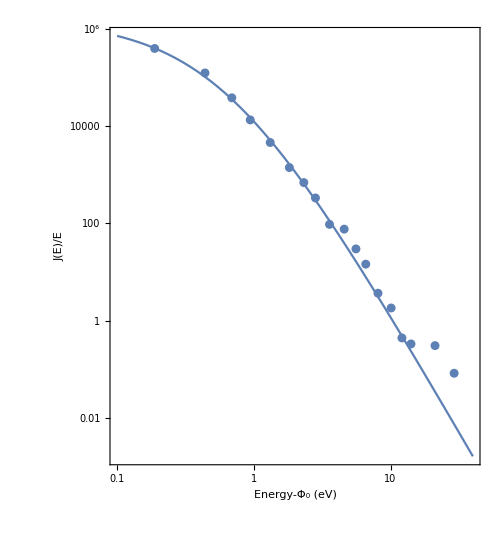

```mathematica
Show[LogLogPlot[FASTModelkeV/.fitter,{en,0.1,40},Frame->True,FrameLabel->{"Energy-Φ_0 (eV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->11/10,ImageSize->500],ListLogLogPlot[eAndFluxkeV]]
```

```mathematica
F=Length@energies[[3;;]]-4;
```

```mathematica
rules=(Append[fitter,en->#/1000]&/@(energies[[startInd;;]]-energies[[startInd-1]]))
```

{{fitT→0.24,fitKappa→35,fitN→0.6,en→0.1882},{fitT→0.24,fitKappa→35,fitN→0.6,en→0.4392},{fitT→0.24,fitKappa→35,fitN→0.6,en→0.6902},{fitT→0.24,fitKappa→35,fitN→0.6,en→0.9412},{fitT→0.24,fitKappa→35,fitN→0.6,en→1.3172},{fitT→0.24,fitKappa→35,fitN→0.6,en→1.8192},{fitT→0.24,fitKappa→35,fitN→0.6,en→2.3202},{fitT→0.24,fitKappa→35,fitN→0.6,en→2.8222},{fitT→0.24,fitKappa→35,fitN→0.6,en→3.5752},{fitT→0.24,fitKappa→35,fitN→0.6,en→4.5782},{fitT→0.24,fitKappa→35,fitN→0.6,en→5.5822},{fitT→0.24,fitKappa→35,fitN→0.6,en→6.5852},{fitT→0.24,fitKappa→35,fitN→0.6,en→8.0912},{fitT→0.24,fitKappa→35,fitN→0.6,en→10.0992},{fitT→0.24,fitKappa→35,fitN→0.6,en→12.1092},{fitT→0.24,fitKappa→35,fitN→0.6,en→14.1092},{fitT→0.24,fitKappa→35,fitN→0.6,en→21.1392},{fitT→0.24,fitKappa→35,fitN→0.6,en→29.1692}}

```mathematica
modelData=(FASTModelkeV/.#)&/@rules
```

{392950.,86990.5,29174.6,12379.9,4484.91,1573.64,687.741,346.086,147.988,59.6786,28.4646,15.253,6.95697,2.96551,1.46804,0.809684,0.166113,0.0466753}

```mathematica
chiSq=1/F * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
```

3.07624

```mathematica
modelData=(FASTModelkeV/.#)&/@rules
```

{394990.,133901.,46847.8,16885.8,3857.51,587.841,98.6977,17.9688,1.60916,0.0815931,0.00518393,0.000401693,0.0000117912,1.72706×10^-7,3.92897×10^-9,1.30218×10^-10,6.38143×10^-15,1.0096×10^-18}

```mathematica
chiSq=1/F * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
```

3.7126

```mathematica
chiSq
```

```mathematica
Sum
```

```mathematica
fitter={fitT->0.240,fitKappa->35,fitN->0.6};
```

```mathematica
chiSqCalc[fitter_]:=Module[{chiSq,rules,modelData},
rules=(Append[fitter,en->#/1000]&/@(energies[[startInd;;]]-energies[[startInd-1]]));
modelData=(FASTModelkeV/.#)&/@rules;
chiSq=1/F * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
];
```

```mathematica
fitterList=({fitT->0.250,fitKappa->#,fitN->0.6})&/@{1.6,1.7,1.8,2.0,2.3,2.5,3.0,3.9,4.2,5.0,10,30}
```

{{fitT→0.25,fitKappa→1.6,fitN→0.6},{fitT→0.25,fitKappa→1.7,fitN→0.6},{fitT→0.25,fitKappa→1.8,fitN→0.6},{fitT→0.25,fitKappa→2.,fitN→0.6},{fitT→0.25,fitKappa→2.3,fitN→0.6},{fitT→0.25,fitKappa→2.5,fitN→0.6},{fitT→0.25,fitKappa→3.,fitN→0.6},{fitT→0.25,fitKappa→3.9,fitN→0.6},{fitT→0.25,fitKappa→4.2,fitN→0.6},{fitT→0.25,fitKappa→5.,fitN→0.6},{fitT→0.25,fitKappa→10,fitN→0.6},{fitT→0.25,fitKappa→30,fitN→0.6}}

```mathematica
(chiSqCalc[#])&/@fitterList
```

{53.5158,49.8582,45.8074,33.2091,16.7284,10.1047,3.02773,1.07879,1.07455,1.29398,2.63764,4.09111}